```mathematica
(*Cosmomathica version 0.1, November 2013. By Adrian Vollmer, Institute for theoretical physics, University Heidelberg.*)
```

## Preamble

```mathematica
BeginPackage["cosmomathica`interface`"]
```

```mathematica
Transfer::usage="Transfer[omegaM, fBaryon, Tcmb, h] provides an interface to Eisenstein & Hu's fitting formula for the transfer function. It takes the reduced total matter density ω_M, the fraction of baryons Ω_b/Ω_M, the CMB temperature and the dimensionless Hubble constant as input, and returns the sound horizon, the wavenumber k_peak where the spectrum has a maximum, the transfer function for CDM, baryons, both, or with no baryons or no wiggles.";

Halofit::usage="Halofit[OmegaM, OmegaL, gammaShape, sigma8, ns, betaP, z0] provides an interface to the halofit algorithm by Robert E. Smith et al. (reimplemented in C by Martin Kilbinger). It takes the total matter density Ω_M, the vacuum energy density Ω_L, a shape factor, σ_8, n_s, β_p, and a fixed redshift z_0 as input, and returns the nonlinear matter power spectrum (computed in three ways: linearly with the BBKS alogorithm, nonlinear with the algorithm by Peacock and Dobbs, or nonlinearly with the Halofit algorithm) at 20 different values of the scale factor and the convergence power spectrum in tabulated form.";

CosmicEmu::usage="CosmicEmu[omegaM, omegaB, sigma8, ns, w] provides an interface to the CosmicEmulator by Earl Lawrence. It takes ω_M, ω_b, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as z, H, d (all at last scattering), and the sound horizon.";

CAMB::usage="CAMB[OmegaC, OmegaB, OmegaL, h, w] provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.";
```

```mathematica
Tcmb::usage="An option for CAMB";
OmegaNu::usage="An option for CAMB";
YHe::usage="An option for CAMB";
MasslessNeutrinos::usage="An option for CAMB";
MassiveNeutrinos::usage="An option for CAMB";
NuMassDegeneracies::usage="An option for CAMB";
NuMassFractions::usage="An option for CAMB";
ScalarInitialCondition::usage="An option for CAMB";
NonLinear::usage="An option for CAMB";
WantCMB::usage="An option for CAMB";
WantTransfer::usage="An option for CAMB";
WantCls::usage="An option for CAMB";
ScalarSpectralIndex::usage="An option for CAMB";
ScalarRunning::usage="An option for CAMB";
TensorSpectralIndex::usage="An option for CAMB";
RatioScalarTensorAmplitudes::usage="An option for CAMB";
ScalarPowerAmplitude::usage="An option for CAMB";
PivotScalar::usage="An option for CAMB";
PivotTensor::usage="An option for CAMB";
DoReionization::usage="An option for CAMB";
UseOpticalDepth::usage="An option for CAMB";
OpticalDepth::usage="An option for CAMB";
ReionizationRedshift::usage="An option for CAMB";
ReionizationFraction::usage="An option for CAMB";
ReionizationDeltaRedshift::usage="An option for CAMB";
TransferHighPrecision::usage="An option for CAMB";
WantScalars::usage="An option for CAMB";
WantVectors::usage="An option for CAMB";
WantTensors::usage="An option for CAMB";
WantZstar::usage="An option for CAMB";
WantZdrag::usage="An option for CAMB";
OutputNormalization::usage="An option for CAMB";
MaxEll::usage="An option for CAMB";
MaxEtaK::usage="An option for CAMB";
MaxEtaKTensor::usage="An option for CAMB";
MaxEllTensor::usage="An option for CAMB";
TransferKmax::usage="An option for CAMB";
TransferKperLogInt::usage="An option for CAMB";
TransferRedshifts::usage="An option for CAMB";
AccuratePolarization::usage="An option for CAMB";
AccurateReionization::usage="An option for CAMB";
AccurateBB::usage="An option for CAMB";
DoLensing::usage="An option for CAMB";
OnlyTransfers::usage="An option for CAMB";
DerivedParameters::usage="An option for CAMB";
MassiveNuMethod::usage="An option for CAMB";
```

```mathematica
CAMB::Eigenstates="NuMassEigenstates and NuMassFractions must have the same length  (can be zero).";
CAMB::InvalidOption="Option `1` is '`2`', but must be one of the following: `3`";
CAMB::Lists="The following options need to be non-empty lists of the same length: `1`";
CAMB::Error="CAMB exited with the following error code: `1`";
Interface::LinkBroken="`1` crashed. See if there is anything useful on stdout.";
Interface::OutsideBounds="Parameter out of bounds. `5` requires `3` <= `1` <= `4`, but you have `1`=`2`.";
Interface::NotInstalled="`1` appears to be unavailable on your system.";
```

## Main

```mathematica
Begin["`Private`"]
```

```mathematica
$location=DirectoryName[$InputFileName];
```

```mathematica
bool2int[b_]:=If[b,1,0];
validatestring[val_,name_,poss_]:=If[!MemberQ[poss,val],Message[CAMB::InvalidOption,name,val,StringJoin@@Riffle[poss,", "]];Abort[]];
validatelimits[val_,name_,lower_,upper_,module_]:=If[!(lower≤val≤upper),Message[Interface::OutsideBounds,name,val,lower,upper,module];Abort[]];
validatelists[list_]:=If[1!=Length@Union[Length/@list],Message[CAMB::Lists,list];Abort[]];
validateresult[x_,name_]:=Switch[x,$Failed,Message[Interface::LinkBroken,name];False,Null,Message[Interface::NotInstalled,name]False,_,True];
```

```mathematica
reshape[list_,dimensions_]:=First[Fold[Partition[#1,#2]&,Flatten[list],Reverse[dimensions]]]
```

### CAMB

```mathematica
CAMB[OmegaC_?NumericQ,OmegaB_?NumericQ,OmegaL_?NumericQ,h_?NumericQ,w_?NumericQ,opts:OptionsPattern[]]:=Module[{j,link,result,resultfloat,resultint,floats,ints,initialcond,nonlinear,massivenu,limits,check,getDimensions,dimensions,array,redshifts},

getDimensions[list_]:=Module[{i,r},
i=1;r={};
While[i<Length@list,AppendTo[r,list[[i+1;;i+list[[i]]]]];i=i+1+list[[i]]];
r];


(*some parameters must be within certain limits*)
limits={{ReionizationFraction,0,1.5},
{OpticalDepth,0,.9},
{h,"h",.2,1.},
{Tcmb,2.7,2.8},
{YHe,.2,.8},
{MasslessNeutrinos,0,3.1},
(*MassiveNeutrinos?*)
{OmegaB,"Ω_B",.001/h^2,1./h^2},
{OmegaC ,"Ω_C",0./h^2,3./h^2}
};


validatelists[OptionValue@{ScalarSpectralIndex,ScalarRunning,TensorSpectralIndex,RatioScalarTensorAmplitudes,ScalarPowerAmplitude}];
validatelists[OptionValue@{NuMassDegeneracies,NuMassFractions}];
validatelimits[Sequence@@If[NumericQ[#[[1]]],#,{OptionValue[#[[1]]],ToString[#[[1]]]}~Join~Rest@#],"CAMB"]&/@limits;

initialcond={"vector","adiabatic","iso_CDM","iso_baryon","iso_neutrino","iso_neutrino_vel"};
nonlinear={"none","pk","lens","both"};
massivenu={"int","trunc","approx","best"};

validatestring[OptionValue[ScalarInitialCondition],"ScalarInitialCondition",initialcond];
validatestring[OptionValue[NonLinear],"NonLinear",nonlinear];
validatestring[OptionValue[MassiveNuMethod],"MassiveNuMethod",massivenu];

floats=Flatten@{OmegaC,OmegaB,OmegaL,h*100,OptionValue[#]&/@{OmegaNu,Tcmb,YHe,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions,ScalarSpectralIndex,ScalarRunning,TensorSpectralIndex,RatioScalarTensorAmplitudes,ScalarPowerAmplitude,PivotScalar,PivotTensor,OpticalDepth,ReionizationRedshift,ReionizationFraction,ReionizationDeltaRedshift,MaxEtaK,MaxEtaKTensor,TransferKmax},Reverse@Sort@OptionValue@TransferRedshifts};

ints=Flatten@{OptionValue[MassiveNeutrinos],Length@OptionValue[NuMassFractions],Position[initialcond,OptionValue[ScalarInitialCondition]][[1,1]]-1,Position[nonlinear,OptionValue[NonLinear]][[1,1]]-1,Length@OptionValue@ScalarSpectralIndex,bool2int/@OptionValue@{DoReionization,UseOpticalDepth,TransferHighPrecision,WantCMB,WantTransfer,WantCls,WantScalars,WantVectors,WantTensors,WantZstar, WantZdrag},OptionValue[#]&/@{OutputNormalization,MaxEll,MaxEllTensor,TransferKperLogInt},Length@OptionValue@TransferRedshifts,bool2int/@OptionValue@{AccuratePolarization,AccurateReionization,AccurateBB,DoLensing,OnlyTransfers,DerivedParameters},Position[massivenu,OptionValue[MassiveNuMethod]][[1,1]]-1};

(*Print[ints,floats];*)
SetDirectory[$location<>"ext/camb"];
link=Install[$location<>"ext/math_link"];
result=Global`CAMBrun[N/@floats,ints];
ResetDirectory[];
If[!validateresult[result,"CAMB"],Return[$Failed];Abort[]];
Uninstall[link];

{resultfloat,resultint}=result;
If[resultint[[1]]≠0,Message[CAMB::Error,resultint[[1]]];Return[$Failed];Abort[]];
resultint=Drop[resultint,1];
dimensions=getDimensions@resultint;

Do[array=Take[resultfloat,Times@@d];
resultfloat=Drop[resultfloat,Times@@d];
AppendTo[resultfloat,reshape[array,d]],{d,dimensions}];

j=2;
DeleteCases[{
CAMB["age"]->resultfloat[[1,1]],
CAMB["zstar"]->resultfloat[[1,2]],
CAMB["rstar"]->resultfloat[[1,3]],
CAMB["100thetastar"]->resultfloat[[1,4]],
CAMB["zdrag"]->resultfloat[[1,5]],
CAMB["rdrag"]->resultfloat[[1,6]],
CAMB["kD"]->resultfloat[[1,7]],
CAMB["100thetaD"]->resultfloat[[1,8]],
CAMB["zEQ"]->resultfloat[[1,9]],
CAMB["100thetaEQ"]->resultfloat[[1,10]],
CAMB["sigma8"]->resultfloat[[-1]],
If[OptionValue[WantScalars],CAMB["CLscalar"]->Transpose@First@Transpose[resultfloat[[j++]]]],
If[OptionValue[WantVectors],CAMB["CLvector"]->Transpose@First@Transpose[resultfloat[[j++]]]],
If[OptionValue[WantTensors],CAMB["CLtensor"]->Transpose@First@Transpose[resultfloat[[j++]]]],
If[OptionValue[WantTransfer],CAMB["redshifts"]->(redshifts=resultfloat[[-2]])],
If[OptionValue[WantTransfer],Sequence@@Flatten@{
CAMB["PSlinear"]->Table[Exp@Transpose@{resultfloat[[j]],resultfloat[[j+1,All,k]]},{k,Length@redshifts}],
CAMB["PSnonlinear"]->Table[Exp@Transpose@{resultfloat[[j]],resultfloat[[j+2,All,k]]},{k,Length@redshifts}
]}~Join~{CAMB["Transfer"]->Table[Transpose[resultfloat[[j+3,All,All,k]]],{k,Length@redshifts}]}
](*,CAMB["ints"]->resultint,CAMB["floats"]->resultfloat*)
},Null]
];
Options[CAMB]={Tcmb->2.7255,OmegaNu->0,YHe->.24,MasslessNeutrinos->3.046,MassiveNeutrinos->0,NuMassDegeneracies->{0},NuMassFractions->{1},ScalarInitialCondition->"adiabatic",NonLinear->"none",WantCMB->True,WantTransfer->True,WantCls->True,ScalarSpectralIndex->{.96},ScalarRunning->{0},TensorSpectralIndex->{0},RatioScalarTensorAmplitudes->{1},ScalarPowerAmplitude->{2.1*^-9},PivotScalar->.05,PivotTensor->.05,DoReionization->True,UseOpticalDepth->False,OpticalDepth->0.,ReionizationRedshift->10.,ReionizationFraction->1.,ReionizationDeltaRedshift->.5,TransferHighPrecision->False,WantScalars->True,WantVectors->True,WantTensors->True,WantZstar->True, WantZdrag->True,OutputNormalization->1,MaxEll->1500,MaxEtaK->3000.,MaxEtaKTensor->800.,MaxEllTensor->400,TransferKmax->.9,TransferKperLogInt->0,TransferRedshifts->{0.},AccuratePolarization->True,AccurateReionization->False,AccurateBB->False,DoLensing->True,OnlyTransfers->False,DerivedParameters->True,MassiveNuMethod->"best"};
Options[validatestring]=Options[CAMB];
```

### Transfer

```mathematica
(*Transfer function*)
Transfer[omegaM_?NumericQ,fBaryon_?NumericQ,Tcmb_?NumericQ,h_?NumericQ]:=Module[{result,link,krange,fitonek,horizon,peak},

link=Install[$location<>"ext/math_link"];

Global`TFSetParameters[N@omegaM,N@fBaryon,N@Tcmb];

fitonek[k_]:={Sequence@@Global`TFFitOneK[k],
Global`TFNoWiggles[N@omegaM,N@fBaryon,N@h,N@Tcmb,k],
Global`TFZeroBaryon[N@omegaM,N@h,N@Tcmb,k]}; 

krange=10^Range[-6.,4.,.01];
result=Transpose[fitonek/@krange];
horizon=Global`TFSoundHorizon[N@omegaM,N@fBaryon,N@h];
peak=Global`TFkPeak[N@omegaM,N@fBaryon,N@h];
validateresult[Global`TFFitOneK[.1],"transfer"];
Uninstall[link];

{Transfer["soundhorizon"]->horizon,
Transfer["peak"]->peak,
Transfer["kvalues"]->krange,
Transfer["full"]->result[[1]],
Transfer["baryon"]->result[[2]],
Transfer["cdm"]->result[[3]],
Transfer["nowiggles"]->result[[4]],
Transfer["zerobaryons"]->result[[5]]}
];
```

### Halofit

```mathematica
Halofit[OmegaM_?NumericQ,OmegaL_?NumericQ,gammaShape_?NumericQ,sigma8_?NumericQ,ns_?NumericQ,betaP_?NumericQ,z0_?NumericQ]:=Module[{link,Tf={},Kappa={},arange,krange,ellrange,labels,limits,parameters,check},
link=Install[$location<>"ext/math_link"];

arange=Most[10^Range[-2,0,.1]]~Join~{.99999};
krange=10^Range[-4,4,.1]*2998;(*halofit uses units c Mpc/h*)
ellrange=10^Range[-2,6,.1];

labels={"Ω_M","Ω_b","σ_8","n_s","Gamma","β_p","z_0"};
limits={{.1,1.5},{.1,1.5},{.1,1.5},{.7,1.3},{0.05,.5},{1.0,2.0},{.2,1.5}};
(*these are soft limits as given by the authors of halofit+. Results may not be reliable if parameters are outside these bounds*)
parameters={OmegaM,OmegaL,sigma8,ns,gammaShape,betaP,z0};

check=(#[[2,1]]<=#[[1]]<=#[[2,2]])&/@Transpose[{parameters,limits}];
Do[If[!check[[i]],Message[Interface::OutsideBounds,labels[[i]],parameters[[i]],limits[[i,1]],limits[[i,2]],"Halofit"]],{i,Length@check}];
If[!And@@check,Abort[]];


Do[
Global`HFSetParameters[N@OmegaM,N@OmegaL,N@gammaShape,N@sigma8,N@ns,N@betaP,N@z0,i];
AppendTo[Tf,Table[Global`HFGetPkNL[a,k],{a,arange},{k,krange}]];
AppendTo[Kappa,Table[Global`HFGetKappa[ell],{ell,ellrange}]],
{i,0,2}];
validateresult[Global`HFGetKappa[10.],"halofit"];
Uninstall[link];

arange[[-1]]=1.;
(*Just return the raw numbers*)
{Halofit["avalues"]->arange,
Halofit["kvalues"]->krange,
Halofit["ellvalues"]->ellrange,
Halofit["kappaBBKS"]->Kappa[[1]],Halofit["BBKS"]->Tf[[1]],
Halofit["kappaPD96"]->Kappa[[2]],Halofit["PD96"]->Tf[[2]],
Halofit["kappaHalofit"]->Kappa[[3]],Halofit["Halofit"]->Tf[[3]]}
];
```

### CosmicEmu

```mathematica
CosmicEmu[omegaM_?NumericQ,omegaB_?NumericQ,sigma8_?NumericQ,ns_?NumericQ,w_?NumericQ]:=Module[{link,result,labels,limits,parameters,check},

labels={"ω_M","ω_b","σ_8","n_s","w"};
limits={{.12,.155},{.0214,.0235},{.85,1.05},{.61,.9},{-1.3,-.7}};
(*these are hard limits as given by the authors of the cosmic emulator - the program will crash if any parameter is outside its bounds*)
parameters={omegaM,omegaB,sigma8,ns,w};

check=(#[[2,1]]<=#[[1]]<=#[[2,2]])&/@Transpose[{parameters,limits}];
Do[If[!check[[i]],Message[Interface::OutsideBounds,labels[[i]],parameters[[i]],limits[[i,1]],limits[[i,2]],"CosmicEmu"]],{i,Length@check}];
If[!And@@check,Abort[]];

link=Install[$location<>"ext/math_link"];
result=Table[{Transpose@Partition[#[[1]],Length@#[[1]]/2],#[[2]]}&@Global`CEGetPkNL[N@omegaM,N@omegaB,N@sigma8,N@ns,N@w,1/a-1],{a,.5,1.,.1}];
 (*CosmicEmu only does these five redshifts, everything else is interpolated*)
validateresult[(result[[All,2]])[[1,4]],"CosmicEmu"];
Uninstall[link];

(*Just return the raw numbers*)
{CosmicEmu["zvalues"]->Table[1/a-1,{a,.5,1.,.1}],
CosmicEmu["pk"]->result[[All,1]],
CosmicEmu["soundhorizon"]->(result[[All,2]])[[1,1]],
CosmicEmu["zlss"]->(result[[All,2]])[[1,2]],
CosmicEmu["dlss"]->(result[[All,2]])[[1,3]],
CosmicEmu["hubblecmb"]->(result[[All,2]])[[1,4]]}
];
```

```mathematica
End[ ]
EndPackage[ ]
```

## Test

```mathematica
<<(NotebookDirectory[]<>"interface.m")
```

```mathematica
hfdata=Halofit[.25,.75,.259,.8,.9,1.,1.5];
hfdata/.Rule[lhs_,rhs_]->lhs
```

{Halofit[avalues],Halofit[kvalues],Halofit[ellvalues],Halofit[kappaBBKS],Halofit[BBKS],Halofit[kappaPD96],Halofit[PD96],Halofit[kappaHalofit],Halofit[Halofit]}

```mathematica
ListLogLogPlot[Transpose[{halofit["ellvalues"]/.hfdata,halofit["kappaPD96"]/.hfdata}],Joined->True,PlotRange->{10^-14,10^-7}]
```

```mathematica
cedata=CosmicEmu[.15,.022,.9,.9,-1];
cedata/.Rule[lhs_,rhs_]->lhs
```

{CosmicEmu[zvalues],CosmicEmu[pk],CosmicEmu[soundhorizon],CosmicEmu[zlss],CosmicEmu[dlss],CosmicEmu[hubblecmb]}

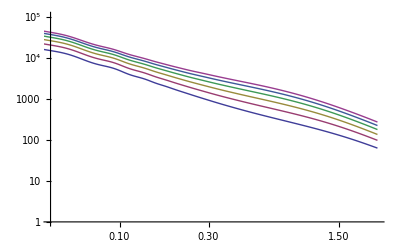

```mathematica
ListLogLogPlot[CosmicEmu["pk"]/.cedata,Joined->True]
```

```mathematica
tfdata=Transfer[.15,.05,2.7,.7];
tfdata/.Rule[lhs_,rhs_]->lhs
```

{Transfer[soundhorizon],Transfer[peak],Transfer[kvalues],Transfer[full],Transfer[baryon],Transfer[cdm],Transfer[nowiggles],Transfer[zerobaryons]}

```mathematica
ListLogLogPlot[Transpose[{transfer["kvalues"],transfer["full"]}/.tfdata],Joined->True]
```

```mathematica
cambdata=CAMB[.2,.05,.75,.6817,-1.,WantTransfer->True,DoLensing->False,NonLinear->"both",WantZstar->False,TransferRedshifts->{0}];
cambdata/.Rule[lhs_,rhs_]->lhs
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[sigma8],CAMB[CLscalar],CAMB[CLvector],CAMB[CLtensor],CAMB[redshifts],CAMB[PSlinear],CAMB[PSnonlinear],CAMB[Transfer],CAMB[ints],CAMB[floats]}

```mathematica
(CAMB["ints"]/.cambdata)
```

{1,10,3,1499,1,3,3,1499,1,4,3,399,1,4,1,106,2,106,10,2,106,10,3,7,106,10,1,10,2,1,1}

```mathematica
(CAMB["floats"]/.cambdata)[[5]]
```

{-11.5562,-11.3598,-11.1635,-10.9671,-10.7708,-10.5744,-10.3781,-10.1818,-9.98542,-9.78907,-9.59273,-9.39639,-9.20004,-9.0037,-8.80736,-8.61101,-8.41467,-8.21833,-8.02198,-7.82564,-7.6293,-7.43295,-7.23661,-7.04027,-6.84392,-6.64758,-6.45124,-6.25489,-6.05855,-5.86221,-5.66586,-5.46952,-5.27318,-5.07683,-4.88049,-4.68415,-4.4878,-4.29146,-4.09512,-3.89877,-3.71645,-3.5623,-3.42877,-3.31099,-3.20563,-3.11032,-3.02331,-2.94326,-2.86916,-2.80016,-2.73562,-2.675,-2.61784,-2.56377,-2.51248,-2.46369,-2.39616,-2.33291,-2.27341,-2.21726,-2.1641,-2.11362,-2.06557,-2.01972,-1.97588,-1.93388,-1.89357,-1.85483,-1.81753,-1.78157,-1.74687,-1.71332,-1.68087,-1.64943,-1.61895,-1.58938,-1.56065,-1.53273,-1.50556,-1.47912,-1.45335,-1.42823,-1.40373,-1.37981,-1.35646,-1.33363,-1.31132,-1.28949,-1.26813,-1.24721,-1.21101,-1.15218,-1.09336,-1.03454,-0.975714,-0.91689,-0.858066,-0.524733,-0.1914,0.141934,0.475267,0.8086,1.14193,1.47527,1.8086,2.14193}

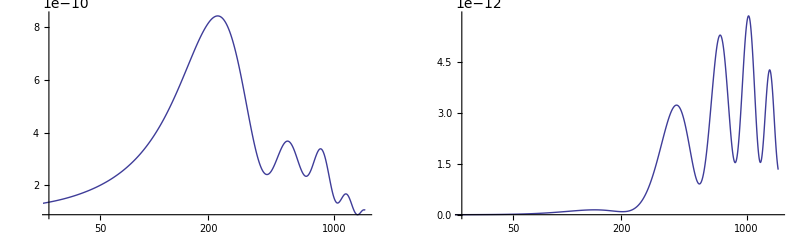

```mathematica
GraphicsGrid@Partition[Table[ListLogLinearPlot[plot,Joined->True,PlotRange->All],{plot,CAMB["CLscalar"]/.cambdata}],2]
```

```mathematica
ListLogLogPlot[({CAMB["PSlinear"],CAMB["PSnonlinear"]}/.cambdata),Joined->True]
```

-Graphics-